#### Define Constants and Equations

```mathematica
Clear["Global`*"]
(*Geometry Consts*)
ID = Quantity[0.004, "Inches"];
L = Quantity[0.3, "Inches"];
Ncap = 231;

rgs = Quantity[0.5,"Centimeters"];

(*Physical Const*)
BoltzmanConst = Quantity[1.380649*^-23, "kg"*("Meters")^2*("s")^-2*("Kelvins")^-1];
IdealGasConst = Quantity[8.314, "Joules"*("Moles")^-1*("Kelvins")^-1];

(*Const, Ar*)
mAr = Quantity[39.948, "amu"];
MAr = Quantity[39.948,"Grams"/"Moles"];
σAr = Quantity[340, "pm"]; (*https://www.omnicalculator.com/physics/mean-free-path*)(*https://web.archive.org/web/20231216044029/https://en.wikipedia.org/wiki/Kinetic_diameter#cite_note-Breck-5*)
ρAr5K = Quantity[1.776,"Grams"*("Centimeters")^-3]; (*https://iopscience.iop.org/article/10.1088/0370-1328/78/6/347*)
ρAr10K = Quantity[1.775,"Grams"*("Centimeters")^-3];
ρAr15K = Quantity[1.773,"Grams"*("Centimeters")^-3];
ρAr20K = Quantity[1.768,"Grams"*("Centimeters")^-3];

(*Get Argon density STP*)
Tstd = Quantity[273.15, "Kelvins"];
Pstd = Quantity[101325, "Pascals"];
ρArSTP = UnitSimplify[Pstd * MAr / (IdealGasConst * Tstd)];

(*Mean Velocity MB dist*)
meanV[T_]:= Sqrt[8*BoltzmanConst*T/(Pi*mAr)];

(*throughput nozzle*)
Qnoz[T_,P_]:=Ncap*P*Pi/12*meanV[T]*ID^3/L

(*Mass flow nozzle/Ar*)
mflow[T_,P_]:=UnitConvert[Qnoz[T,P]*MAr/(T*IdealGasConst),"g"/"Hours"]

(*Growth rate*)
hdot[T_,P_,ρ_] := UnitConvert[mflow[T,P]*1/(ρ*Pi*rgs^2),"Micrometers"/"Hours"]

(*Mean Free Path*)
λAr[T_,P_]:=UnitConvert[BoltzmanConst/(Sqrt[2]*Pi*σAr^2)*T/P,"Micrometers"]

(*Flow SCCM*)
FlowMdotToSCCM[mdot_]:=UnitConvert[mdot/ρArSTP,("Centimeters")^3/"Minutes"]
FlowSCCMToMdot[FlowSCCM_]:=UnitConvert[ρArSTP*FlowSCCM,"g"/"s"]

(*SCCM to hdot*)
FlowSCCMToHdot[FlowSCCM_,ρ_]:=UnitConvert[FlowSCCMToMdot[FlowSCCM]*1/(ρ*Pi*rgs^2),"Micrometers"/"Hours"]
hdotToSCCM[hdot_,ρ_]:=UnitConvert[ρ*Pi*rgs^2/ρArSTP*hdot,("Centimeters")^3/"Minutes"]
```

```mathematica
hdotToSCCM[Quantity[1,"Micrometers"/"Hours"],ρAr5K]
hdotToSCCM[Quantity[10,"Micrometers"/"Hours"],ρAr5K]
hdotToSCCM[Quantity[100,"Micrometers"/"Hours"],ρAr5K]
```

0.00130431 cm^3/min

0.0130431 cm^3/min

0.130431 cm^3/min

```mathematica
Tnozzle = Quantity[273+200, "Kelvins"];
Poven = Quantity[0.07, "Torr"];
FlowSCCM = Quantity[0.01,("Centimeters")^3/"Minutes"];

λAr[Tnozzle,Poven]

mflow[Tnozzle,Poven];

hdot[Tnozzle,Poven,ρAr10K]

FlowSCCMToHdot[FlowSCCM,ρAr10K];
```

1362.45 μm

10.2027 μm/h

```mathematica
Quantity[10^16,1/("cm")^3]*Quantity[0.07,"Torr"]/Quantity[2.67*10^22,1/("cm")^3]
```

2.62172×10^-8 Torr

```mathematica
Solve[2*^-8 == 10^(4.312-4040/T)*760,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→271.291}}

#### Plot growth rate with mean free path limit lines

```mathematica
hdotAr5K[tempC_?NumericQ, pTorr_?NumericQ] :=
 QuantityMagnitude[
  hdot[
   Quantity[tempC, "DegreesCelsius"],
   Quantity[pTorr, "Torr"],
   ρAr5K
  ],
  "Micrometers"/"Hours"
 ];
```

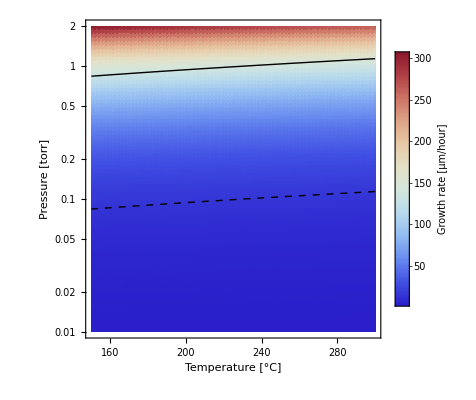

```mathematica
Show[
 DensityPlot[
  hdotAr5K[tempC, 10^logP],
  {tempC, 150, 300},
  {logP, Log10[0.01], Log10[2]},
  FrameLabel -> {
    "Temperature [°C]",
    "Pressure [torr]"
  },
  FrameTicks -> {
    Automatic,
    Table[{Log10[p], ToString[p]}, {p, {0.01, 0.02, 0.05, 0.1, 0.2, 0.5, 1,2}}]
  },
  PlotLegends -> BarLegend[
    Automatic,
    LegendLabel -> "Growth rate [μm/hour]"
  ],
  ColorFunction -> "ThermometerColors",
  PlotPoints -> 80,
  MaxRecursion -> 3
 ],

 ContourPlot[
  QuantityMagnitude[
    λAr[
      Quantity[tempC, "DegreesCelsius"],
      Quantity[10^logP, "Torr"]
    ] - UnitConvert[ID, "Micrometers"],
    "Micrometers"
  ],
  {tempC, 150, 300},
  {logP, Log10[0.01], Log10[2]},
  Contours -> {0},
  ContourStyle -> {Thick, Black},
  ContourShading -> None,  
  PlotPoints -> 80,
  MaxRecursion -> 3
 ],
 
 ContourPlot[
  QuantityMagnitude[
    λAr[
      Quantity[tempC, "DegreesCelsius"],
      Quantity[10^logP, "Torr"]
    ] - UnitConvert[10*ID, "Micrometers"],
    "Micrometers"
  ],
  {tempC, 150, 300},
  {logP, Log10[0.01], Log10[1]},
  Contours -> {0},
  ContourStyle -> {Thick, Black,Dashed},
  ContourShading -> None,  
  PlotPoints -> 80,
  MaxRecursion -> 3
 ]
]
```

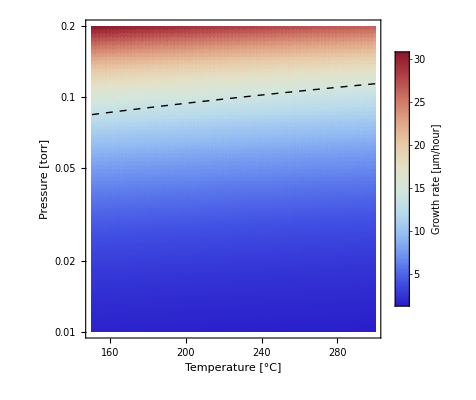

```mathematica
Show[
 DensityPlot[
  hdotAr5K[tempC, 10^logP],
  {tempC, 150, 300},
  {logP, Log10[0.01], Log10[0.2]},
  FrameLabel -> {
    "Temperature [°C]",
    "Pressure [torr]"
  },
  FrameTicks -> {
    Automatic,
    Table[{Log10[p], ToString[p]}, {p, {0.01, 0.02, 0.05, 0.1, 0.2}}]
  },
  PlotLegends -> BarLegend[
    Automatic,
    LegendLabel -> "Growth rate [μm/hour]"
  ],
  ColorFunction -> "ThermometerColors",
  PlotPoints -> 80,
  MaxRecursion -> 3
 ],
 
 ContourPlot[
  QuantityMagnitude[
    λAr[
      Quantity[tempC, "DegreesCelsius"],
      Quantity[10^logP, "Torr"]
    ] - UnitConvert[10*ID, "Micrometers"],
    "Micrometers"
  ],
  {tempC, 150, 300},
  {logP, Log10[0.01], Log10[0.2]},
  Contours -> {0},
  ContourStyle -> {Thick, Black,Dashed},
  ContourShading -> None,  
  PlotPoints -> 80,
  MaxRecursion -> 3
 ]
]
```